## Modules

```mathematica
DiploidSelection[Fgenotypes_,pars_]:=
Block[{i,out=Table[0,{i,1,Length[Genotypes]}]},
For[i=1, i≤Length[Fgenotypes],++i,
out[[i]]=Fgenotypes[[i]]*#Fitness &[pars] [[i]];
];
out/Total[out]
]
```

```mathematica
Drive[Fgenotypes_,pars_]:=
Block[{i,j,out=Table[0,{i,1,Length[#Genotypes &[pars]]}]},
#DriveMatrix.Fgenotypes &[pars]
]
```

```mathematica
Recombination[Fgenotypes_,pars_]:=Block[
{i,j,k,n,newGamete,rec,nrec,out=Table[0,{i,1,Length[#Gametes &[pars]]}]},
n=Length[#Loci &[pars]];
rec={Array[List,ConstantArray[2,n],0,##&]};
For[i=1,i≤Length[Fgenotypes],++i,
For[j=1,j≤Length[rec],++j,
newGamete=Table[0,{i,1,n}];
For[k=1,k≤Length[#Loci &[pars]],++k,
newGamete[[k]]=#Genotypes &[pars] [[i]][[rec[[j]][[k]]+1]][[k]];
];
nrec=Length[SequenceCases[rec[[j]],{0,1}]]+
Length[SequenceCases[rec[[j]],{1,0}]];
out[[Position[#Gametes &[pars],newGamete][[1,1]]]]+=1/2 Fgenotypes[[i]](#recombination)^nrec(1-#recombination)^(Length[#Loci &[pars]]-1-nrec) &[pars];
];
];
out
]
```

```mathematica
Mutation[Fgametes_,pars_]:=Block[{i,j,out=ConstantArray[0,Length[Fgametes]],Fgenotypes,FgenotypesPrime},
Assert[Total[Fgametes]==1];
#MutationMatrix.Fgametes &[pars]
]
```

```mathematica
GameteRecombinants[gamete1_,gamete2_,pars_]:=Block[{out={},rtuples,i},
rtuples=Tuples[{gamete1,gamete2},Length[#Loci]]  &[pars];
For[i=1,i≤Length[rtuples],++i,
AppendTo[out,Table[#Gametes &[pars][[rtuples[[i]][[j]]]][[j]],{j,1,Length[#Loci &[pars]]}]] 
];
out
]
```

```mathematica
ConvertToGenotypes[Fgametes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Genotypes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[i]]=Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[1]]][[1,1]]]]*Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[2]]][[1,1]]]]
];
out
]
```

```mathematica
ConvertToGametes[Fgenotypes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Gametes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[1]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[2]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
];
out
]
```

```mathematica
MakeSingleDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,j,locations,postDriveGenotype,out},
out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray];
Assert[Length[WhoCutsWho]==2];
Assert[WhoCutsWho[[1]]≠WhoCutsWho[[2]]];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],WhoCutsWho[[1]]],
locations=Position[#Genotypes &[pars][[i]], WhoCutsWho[[2]]];
For[j=1,j≤Length[locations],++j,
postDriveGenotype=#Genotypes &[pars][[i]];
postDriveGenotype[[locations[[j]][[1]]]][[locations[[j]][[2]]]]=postDriveGenotype[[Mod[locations[[j]][[1]],2]+1]][[locations[[j]][[2]]]];
out[[i,i]]=1-d;
out[[i,Position[#Genotypes &[pars],postDriveGenotype][[1,1]]]]=d;
If[Position[#Genotypes &[pars],postDriveGenotype][[1,1]]==i,out[[i,i]]=1];
];
];
];
Transpose[out]
]

MakeDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoCutsWho],++i,
out =MakeSingleDriveMatrix[WhoCutsWho[[i]],pars,d].out
];
out
]
```

```mathematica
MakeSingleMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,j,locations,postMutationGamete,out},
out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray];
For[i=1,i≤Length[#Gametes &[pars]],++i,
locations=Position[#Gametes &[pars][[i]], WhoMutatesToWho[[1]]];
For[j=1,j≤Length[locations],++j,
postMutationGamete=#Gametes &[pars][[i]];
postMutationGamete[[locations[[j]]]] = WhoMutatesToWho[[2]];
out[[i,i]]=1-μ;
out[[i,Position[#Gametes &[pars],postMutationGamete][[1,1]]]]=μ;
If[Position[#Gametes &[pars],postMutationGamete][[1,1]]==i,out[[i,i]]=1];
]
];
Transpose[out]
]

MakeMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoMutatesToWho],++i,
out =MakeSingleMutationMatrix[WhoMutatesToWho[[i]],pars,μ].out
];
out
]
```

```mathematica
MakeFitnessMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]*=(1-s)^Length[Position[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]]]];
];
];
W
]
```

```mathematica
MakeDominantPayloadMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]=(1-s)];
];
];
W
]
```

```mathematica
MakeRecessivePayloadMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
If[2==Count[Flatten[#Genotypes &[pars][[i]]],Payload[[1]]]&&2==Count[Flatten[#Genotypes &[pars][[i]]],Payload[[2]] ],
 W[[i]]=(1-s)];
];
W
]
```

```mathematica
Make2LocusUnderDominanceFitnessMatrix[allele_,pars_,s_]:=Block[{W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],allele[[2]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[1]]],
 W[[i]]=(1-s)];
If[MemberQ[Flatten[Genotypes[[i]]],allele[[1]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[2]]],
 W[[i]]=(1-s)];
];
W
]
```

```mathematica
GametesToAlleleFrequency[Gametes_,pars_]:=Block[{i,j,LociFreq,pos},
LociFreq=Table[0,{i,1,Length[#Loci &[pars]]},{j,1,2}];
For[i=1,i≤Length[#Gametes &[pars]],++i,
For[j=1,j≤Length[#Loci &[pars]],++j,
pos=Position[#Loci &[pars],#Gametes &[pars][[i]][[j]]];
LociFreq[[pos[[1,1]]]][[pos[[1,2]]]]+=Gametes[[i]];
];
];
LociFreq
]
```

Compare to Sally

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
Wpayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0];
Wtoxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Ad"},pars,1];
W={1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s};
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"recombination"->r|>;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm;
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,d]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

Function::slot1: (#Genotypes&)[pars] is expected to have an Association as the first argument.

General::stop: Further output of Function::slot1 will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Genotypes].

Function::slot1: (#Genotypes&)[pars] is expected to have an Association as the first argument.

Set::partw: Part 2 of {1} does not exist.

Set::partw: Part 3 of {1} does not exist.

Set::partw: Part 5 of {1} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

SparseArray[<36>, {16, 16}]

```mathematica
Clear[F]
Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars][[1]]//Simplify
```

(F[1]^2-(-1+d)^2 r (-1+h s) F[2] F[3]-(-1+d) F[1] (ϵ (F[2]+F[3]-h s F[3])-(-1+d) (-1+r) (-1+h s) F[4]))/(F[1]^2+2 F[2] F[3]-2 h s F[2] F[3]+ϵ (F[2]^2-(-1+s) F[3]^2)+2 F[2] F[4]-2 h s F[2] F[4]+2 F[3] F[4]-2 s F[3] F[4]+F[4]^2-s F[4]^2+2 F[1] (ϵ (F[2]+F[3]-h s F[3])+F[4]-h s F[4]))

```mathematica
(*Sally:*)
```

```mathematica
(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))
```

(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))

## Multiplicative payload

```mathematica
0.99*0.99*1.1
```

1.07811

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeMultiplicativeMatrix[{"Cd","Dd"},pars,spl];
FitnessDrive=MakeMultiplicativeMatrix[{"Ad","Bd"},pars,sd];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,e];
Fitness=FitnessPayload*FitnessToxin*FitnessDrive;
```

```mathematica
ClearAll[foo]
foo=RawBoxes[Replace[ToBoxes@#,InterpretationBox[a_,b_,c___]:>With[{aa=StringReplace[a,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow"}]},aa],{0,Infinity}]]&;

foo@CForm[{1,(1-e) (1-spl),(1-e) (1-spl),1-spl,1-sd,(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),1-sd,(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-spl),(1-e) (1-spl),1-spl,1-spl,(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-spl),1-spl,(1-e) (1-spl),1-spl,(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),1-spl,1-spl,1-spl,1-spl,(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),1-sd,(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3,(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),1-sd,(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3,(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd) (1-spl),(1-sd) (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd) (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^2,(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3,(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3,(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^4,(1-e) (1-sd)^4 (1-spl),(1-e) (1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^4 (1-spl),(1-e) (1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-e) (1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-e) (1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^2 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^3 (1-spl),(1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-sd)^4 (1-spl),(1-sd)^4 (1-spl)}]
```

List(1,(1 - e)*(1 - spl),(1 - e)*(1 - spl),1 - spl,1 - sd,(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),1 - sd,(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*(1 - spl),(1 - e)*(1 - spl),1 - spl,1 - spl,(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*(1 - spl),1 - spl,(1 - e)*(1 - spl),1 - spl,(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),1 - spl,1 - spl,1 - spl,1 - spl,(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),1 - sd,(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),1 - sd,(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),(1 - sd)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,2),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,4),(1 - e)*pow(1 - sd,4)*(1 - spl),(1 - e)*pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,4)*(1 - spl),(1 - e)*pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),(1 - e)*pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),(1 - e)*pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,2)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,3)*(1 - spl),pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl),pow(1 - sd,4)*(1 - spl))

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Drive
```

```mathematica
it=Drive[Table[F[i],{i,0,Length[Genotypes]-1}],pars];
```

```mathematica
Format[F[a_],CForm]:=HoldForm[F[[a]]]
it/.(1-d)^2->OneMinusdd/.d^2->dd/.(1-d)^3->OneMinusddd/.d^3->ddd//CForm//Simplify;
```

```mathematica
Format[F2[a_],CForm]:=HoldForm[F2[[a]]]
ClearAll[foo]
foo=RawBoxes[Replace[ToBoxes@#,InterpretationBox[a_,b_,c___]:>With[{aa=StringReplace[a,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow"}]},aa],{0,Infinity}]]&;
it=ConvertToGenotypes[Recombination[Table[F2[i],{i,0,Length[Genotypes]-1}],pars],pars];
```

```mathematica
foo@CForm[it[[193;;256]]/.(1-r)^3->OneMinusrrr/.(1-r)^2->OneMinusrr/.r^2->rr/.r^3->rrr];
```

```mathematica
Export["squared.c",Compile[{x},x^2]]
```

squared.c

```mathematica
SystemOpen["squared.c"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["squared.c"]]]
```

```mathematica
256/4
```

64

Read SimData

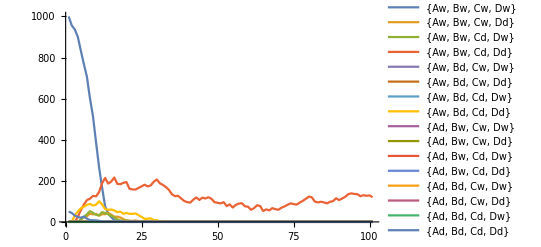

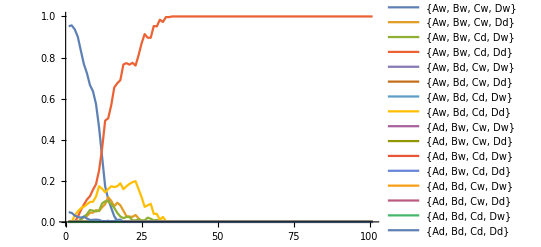

```mathematica
Data=Import["C:\\Users\\Freek\\Documents\\GeneDrive\\Data\\sim_results.csv"];
Data2=Table[ConvertToGametes[Data[[i,;;]],pars],{i,2,Length[Data]}];
ListLinePlot[Transpose[Data2],PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}],PlotRange->All]
Data3=Table[Normalize[Data2[[i,;;]],Total],{i,1,Length[Data2]}];
ListLinePlot[Transpose[Data3],PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}],PlotRange->All]
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessDrive=MakeFitnessMatrix[{"Ad","Bd"},pars,0.1];
Fitnesspayload=MakeFitnessMatrix[{"Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessDrive*FitnessToxin*Fitnesspayload;

DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

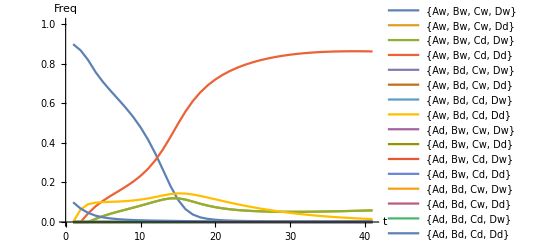

```mathematica
plot1=ListLinePlot[Transpose[Table[F[t],{t,0,40}]],PlotRange->{Automatic,{0,1.01}},AxesLabel->{"t","Freq"},PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
Data=Import["C:\\Users\\Freek\\Documents\\GeneDrive\\Data\\sim_results.csv","FieldSeparators"->" "];
```

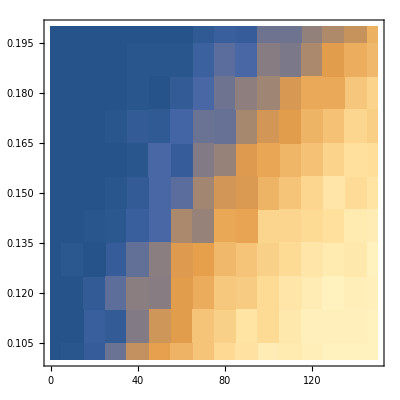

```mathematica
ListDensityPlot[Data,InterpolationOrder->0]
```